```mathematica
(* Sets the Base directory, changing which files are easiest to acces. *)
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns","18-03-18_100mTorrBGP","data"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];

(* The folder that contains the different data runs to analyze, this folder contains subfolders with 
individual runs.*)
dataFolder=FileNameJoin[{folder}]
SetDirectory[dataFolder];
(* Make a list of directories to easily select the folder you would like to work with.*)
directories=Select[FileNames["*","",1],DirectoryQ];
For[i=Length[directories],i>0,i--,
Print[i -> directories[[i]]];]
(* set rootFolder to the folder name containing the desired Files *)
rootFolder=FileNameJoin[{dataFolder}];
SetDirectory[rootFolder];
(* Obtain the filenames of the rotation data and print them out.*)
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
rotationFiles=FileNames["FDayRotation"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
```

/home/karl/Dropbox/00School/research/DataRuns/18-03-18_100mTorrBGP/data

## Inputting data from Timestamps

```mathematica
(*Input the timestamps of the no pump files in the following array*)
runs100BGP=<|pre93->"040513",post93-> "051352",pre96->"062812",post96->"073649",pre99->"085104",post99->"095943",pre103->"111408",post103->"124923"|>
runs700BGPlowTemp=<|pre102->"165236",post102->"180119",pre105->"191618",post105->"202505",pre108->"214015",post108->"224901",pre111->"000400"|>;
runs700BGPhighTemp=<|pre125->"014133",post125->"025011",pre130->"040525",post130->"051409",pre135->"062916",post135->"073802",pre140->"085258",post140->"100141"|>
secondPop700BGPhighTemp=<|pre140sec->"122315",post140sec->"130450",pre137sec->"143712",post137sec->"155325",post136pt5->"184723",pre136pt5-> "173236",pre135pt5->"200807",post135pt5->"212254"|>
runs500BGP=<|pre135p5->"231936",post135p5->"001127",pre132p5->"013130",post132p5->"022317",pre129p5->"034332",post129p5->"043529",pre126p5->"055540",post126p5->"064738",
pre123p5->"080744",post123p5->"085941",
pre120p5->"101943",post120p5->"111137",
pre117p5->"123147",post117p5->"132345"
|>;
runs100BGP2=
<|pre103r2->"184551",post103r2->"193746",
pre100r2->"205810",post100r2->"215024",
pre97r2->"231045",post97r2->"000238",
pre94r2->"012302",post94r2->"021504",
pre91r2->"033520",post91r2->"042718",
pre88r2->"054738",post88r2->"063935",
pre85r2->"080009",post85r2->"085207",
pre82r2->"101236"|>




fileTimestamp=Join[runs100BGP,runs700BGPlowTemp,runs700BGPhighTemp,secondPop700BGPhighTemp,runs500BGP,runs100BGP2]
(* Record the baseline angle, the angle of the probe polarization when the magnets are off and the pump laser is off *)
baselineAngle=.225;

(* Iterates through each of the timestamps above and calculates the number density from the Faraday Rotation data. *)
pdata={};
ndata={};
For[i=1,i≤Length[fileTimestamp],i++,
ndataLine=ProcessFaradayScanFile[scanFiles,fileTimestamp[[i]],baselineAngle];
AppendTo[ndata,ndataLine];
pdataLine=ProcessRbPolarizationFileSequence[scanFiles,fileTimestamp[[i]],baselineAngle,3];
AppendTo[pdata,pdataLine];

];

nstuff=Dataset[ndata];
pstuff=Dataset[pdata];
```

<|pre93→040513,post93→051352,pre96→062812,post96→073649,pre99→085104,post99→095943,pre103→111408,post103→124923|>

<|pre125→014133,post125→025011,pre130→040525,post130→051409,pre135→062916,post135→073802,pre140→085258,post140→100141|>

<|pre140sec→122315,post140sec→130450,pre137sec→143712,post137sec→155325,post136pt5→184723,pre136pt5→173236,pre135pt5→200807,post135pt5→212254|>

<|pre103r2→184551,post103r2→193746,pre100r2→205810,post100r2→215024,pre97r2→231045,post97r2→000238,pre94r2→012302,post94r2→021504,pre91r2→033520,post91r2→042718,pre88r2→054738,post88r2→063935,pre85r2→080009,post85r2→085207,pre82r2→101236|>

<|pre93→040513,post93→051352,pre96→062812,post96→073649,pre99→085104,post99→095943,pre103→111408,post103→124923,pre102→165236,post102→180119,pre105→191618,post105→202505,pre108→214015,post108→224901,pre111→000400,pre125→014133,post125→025011,pre130→040525,post130→051409,pre135→062916,post135→073802,pre140→085258,post140→100141,pre140sec→122315,post140sec→130450,pre137sec→143712,post137sec→155325,post136pt5→184723,pre136pt5→173236,pre135pt5→200807,post135pt5→212254,pre135p5→231936,post135p5→001127,pre132p5→013130,post132p5→022317,pre129p5→034332,post129p5→043529,pre126p5→055540,post126p5→064738,pre123p5→080744,post123p5→085941,pre120p5→101943,post120p5→111137,pre117p5→123147,post117p5→132345,pre103r2→184551,post103r2→193746,pre100r2→205810,post100r2→215024,pre97r2→231045,post97r2→000238,pre94r2→012302,post94r2→021504,pre91r2→033520,post91r2→042718,pre88r2→054738,post88r2→063935,pre85r2→080009,post85r2→085207,pre82r2→101236|>

General::prng: Value of option PlotRange -> {-0.01+Min[{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-20.941,0.237319},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Max,2],{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-«19»,«20»},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Min,2]],«5»+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::prng: Value of option PlotRange -> {-0.01+Min[{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-20.941,0.237319},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Max,2],{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-«19»,«20»},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Min,2]],«5»+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {-0.01+Min[{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-20.941,0.237319},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Max,2],{{-36.9719,0.227725},{-37.6359,0.228111},{-36.8297,0.229441},{-21.937,0.23655},{-«19»,«20»},{-20.2769,0.238344},{-11.7866,0.264492},{-10.6008,0.269451},{-9.79439,0.276372}}[Min,2]],«5»+«1»} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of General::prng will be suppressed during this calculation.

```mathematica
pstuff[SortBy["time"]](*[Select[120>#["CurrTemp(Res)"]≥114&]]*)
nstuff[SortBy["time"]]
```

Dataset[<>]

Dataset[<>]

```mathematica
nstuff[All,{"Comments","n_rb","plot"}]
```

Dataset[<>]

```mathematica
Export["nrbVsTres.tsv",nstuff]
```

nrbVsTres.tsv

## Generating n_Rb Graphs

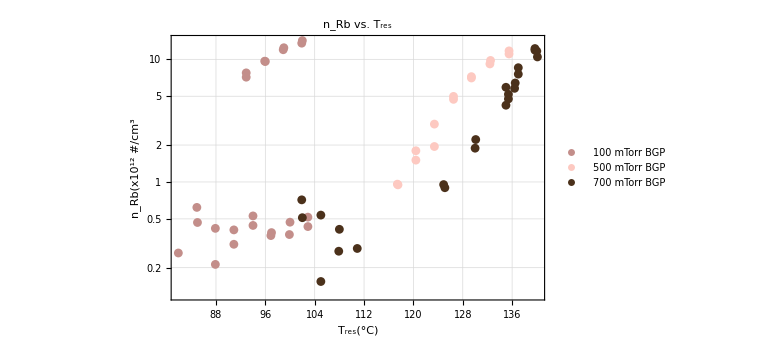

```mathematica
nVsTplotLabels={PlotLabel->"n_Rb vs. T_res",FrameLabel->{"T_res(°C)","n_Rb(x10^12 #/cm^3"}};
nVsBGPplotLabels={PlotLabel->"n_Rb vs. P_N_2",FrameLabel->{"P_N_2(torr)","n_Rb(x10^12 #/cm^3"}};

(* Plot n_Rb vs. BGP 
nvBGP=nstuff[All,{"CVGauge(N2)(Torr)","n_rb"}];
*)
nvT100=nstuff[Select[#["CVGauge(N2)(Torr)"]<.200&]][All,{"CurrTemp(Res)","n_rb"}];
nvT500=nstuff[Select[#["CVGauge(N2)(Torr)"]>.200&&#["CVGauge(N2)(Torr)"]<.6 &]][All,{"CurrTemp(Res)","n_rb"}];
nvT700=nstuff[Select[#["CVGauge(N2)(Torr)"]>.600&&#["CVGauge(N2)(Torr)"]<.9 &]][All,{"CurrTemp(Res)","n_rb"}];
ListLogPlot[{Legended[nvT100,"100 mTorr BGP"],Legended[nvT500,"500 mTorr BGP"],Legended[nvT700,"700 mTorr BGP"]},nVsTplotLabels,PlotStyle->18,LabelStyle->20,Frame->True,GridLines->Automatic,ImageSize->Large]
```

```mathematica
pstuffSave=pstuff;
```

## Generating P_Rb Graphs

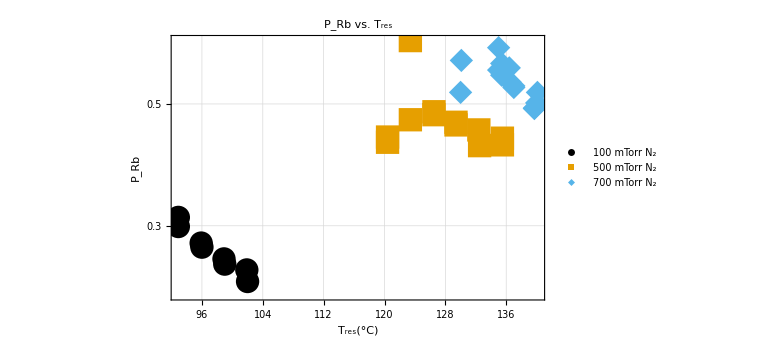

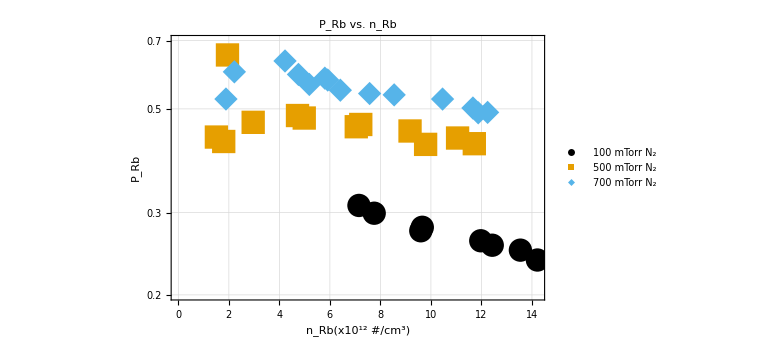

```mathematica
pVsTplotLabels={PlotLabel->"P_Rb vs. T_res",FrameLabel->{"T_res(°C)","P_Rb"}};
pVsnplotLabels={PlotLabel->"P_Rb vs. n_Rb",FrameLabel->{"n_Rb(x10^12 #/cm^3)","P_Rb"}};

(* Selecting out different buffer gas pressures 
pVt275=pstuff[Select[#["CVGauge(N2)(Torr)"]<.3&]][All,{"CurrTemp(Res)","p_rb"}];
pVt500=pstuff[Select[#["CVGauge(N2)(Torr)"]≥.3&]][All,{"CurrTemp(Res)","p_rb"}]
pVn275=pstuff[Select[#["CVGauge(N2)(Torr)"]<.3&]][All,{"n_rb","p_rb"}];
pVn500=pstuff[Select[#["CVGauge(N2)(Torr)"]≥.3&]][All,{"n_rb","p_rb"}]

Plotting the selected gas Pressures
ListPlot[{Legended[pVn275,"275 mTorr N_2"],Legended[pVn500,"500 mTorr N_2"]},pVsnplotLabels]
ListPlot[{Legended[pVt275,"275 mTorr N_2"],Legended[pVt500,"500 mTorr N_2"]},pVsTplotLabels]
*)
pstuff=pstuff[Select[#["n_rb"]>1&]];
pvT100=pstuff[Select[#["CVGauge(N2)(Torr)"]<.200&]][All,{"CurrTemp(Res)","p_rb"}];
pvT500=pstuff[Select[#["CVGauge(N2)(Torr)"]>.200&&#["CVGauge(N2)(Torr)"]<.6 &]][All,{"CurrTemp(Res)","p_rb"}];
pvT700=pstuff[Select[#["CVGauge(N2)(Torr)"]>.600&&#["CVGauge(N2)(Torr)"]<.9 &]][All,{"CurrTemp(Res)","p_rb"}];

ListLogPlot[{Legended[pvT100,"100 mTorr N_2"],Legended[pvT500,"500 mTorr N_2"],Legended[pvT700,"700 mTorr N_2"]},pVsTplotLabels,PlotStyle->colorBlindPallete,PlotMarkers->{Automatic,24},LabelStyle->20,Frame->True,GridLines->Automatic,ImageSize->Large]

pvn100=pstuff[Select[#["CVGauge(N2)(Torr)"]<.200&]][All,{"n_rb","p_rb"}];
pvn500=pstuff[Select[#["CVGauge(N2)(Torr)"]>.200&&#["CVGauge(N2)(Torr)"]<.6 &]][All,{"n_rb","p_rb"}];
pvn700=pstuff[Select[#["CVGauge(N2)(Torr)"]>.600&&#["CVGauge(N2)(Torr)"]<.9 &]][All,{"n_rb","p_rb"}];

ListLogPlot[{Legended[pvn100,"100 mTorr N_2"],Legended[pvn500,"500 mTorr N_2"],Legended[pvn700,"700 mTorr N_2"]},pVsnplotLabels,PlotMarkers->{Automatic,24},LabelStyle->20,Frame->True,GridLines->Automatic,ImageSize->Large,PlotStyle->colorBlindPallete,PlotRange->{Automatic,{.2,.7}}]
```

## Faraday Rotations

### Only Number Density Over Time

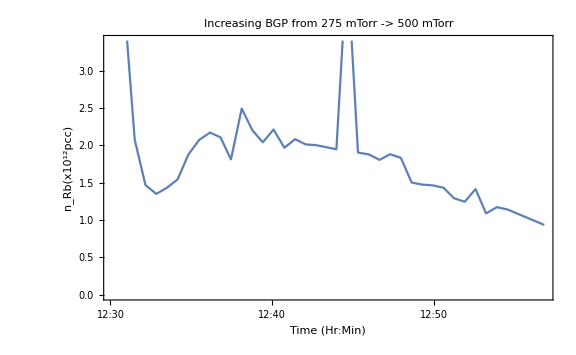

```mathematica
firstFileTimestamp="221152";
numberOfFiles=38;
numDenData=ProcessNumberDensityOverTime[rotationFiles,firstFileTimestamp,baselineAngle,numberOfFiles];
DateListPlot[numDenDataset[All,{"time",#["n_rb"]/1*^12&}],PlotLabel->"Increasing BGP from\n275 mTorr -> 500 mTorr",FrameLabel->{"Time (Hr:Min)","n_Rb(x10^12pcc)"},LabelStyle->18,ImageSize->Large]
```

### Polarization Over Time

Dataset[<>]

Dataset[<>]

Dataset[<>]

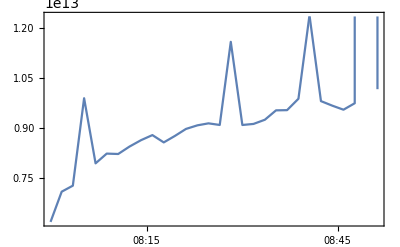

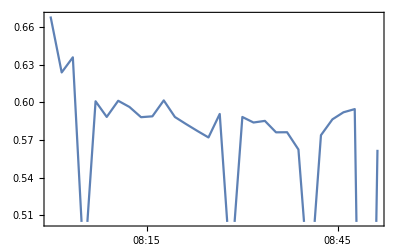

```mathematica
numberOfFiles=3;
files=rotationFiles;
baselineAngle=.225;

delta125to130="031207";
delta130to135="053608";
delta135to140="075956";
data=ProcessQuickPolarizationOverTime[rotationFiles,delta135to140,baselineAngle,numberOfFiles,30];
dataset=Dataset[data]
nVsTime=dataset[All,{"time","n"}]
pVsTime=dataset[All,{"time","prbSPlus"}]
temp120To125BGP500=nVsTime;
DateListPlot[Normal[nVsTime]]
DateListPlot[Normal[pVsTime]]
```

### Get Baseline Angle From Varying Magnetic Field

Dataset[<>]

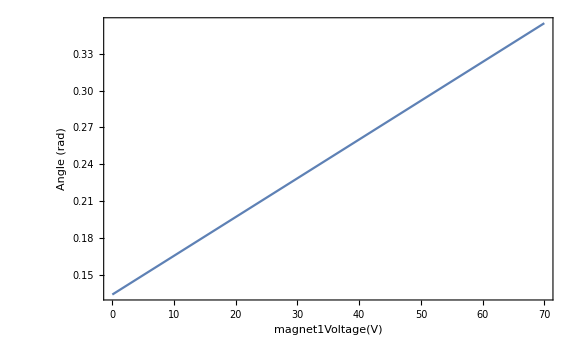

0.134456

θ_o= 0.134456

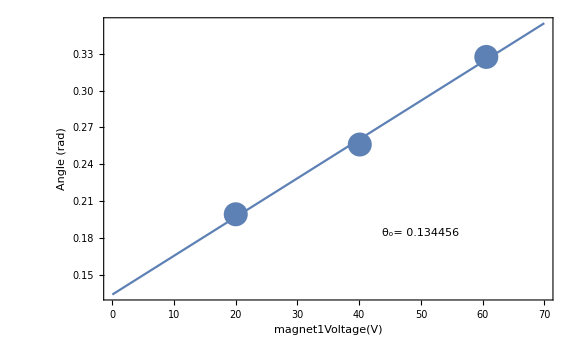

```mathematica
magFieldData=ProcessNumberDensityOverTime[rotationFiles,"121452",baselineAngle,16];
faradayRotationDataset=Dataset[magFieldData][Select[StringContainsQ[#Comments,"no pump"]&]];
yAxis="Angle (rad)";
xAxis="magnet1Voltage(V)";
selectedData=faradayRotationDataset[2;;4,{xAxis,yAxis}]
modelFit=LinearModelFit[Normal[selectedData[All,Values]],x,x];
plotFit=Plot[modelFit[x],{x,0,70},FrameLabel->{xAxis,yAxis}]
modelFit[0]
zeroString="θ_o= "<>ToString[modelFit[0]]
Show[{plotFit,ListPlot[selectedData,FrameLabel->{xAxis,yAxis}],Graphics[Text[zeroString,{50,modelFit[0]+.05}],BaseStyle->15]}]
```

## Initialization Cells

```mathematica
black=RGBColor[0/255,0/255,0/255];
orange=RGBColor[230/255,159/255,0];
skyBlue=RGBColor[86/255,180/255,233/255];
bluishGreen=RGBColor[0/255,158/255,115/255];
yellow=RGBColor[240/255,228/255,66/255];
blue=RGBColor[0/255,114/255,178/255];
vermillion=RGBColor[213/255,94/255,0/255];
reddishPurple=RGBColor[204/255,121/255,167/255];

colorBlindPallete={orange,skyBlue,bluishGreen,yellow,blue,vermillion,reddishPurple,black}; (*The standard order*)
colorBlindPallete={black,orange,skyBlue,yellow,reddishPurple,vermillion,blue,bluishGreen}; (*Works well with laser goggles*)

SetOptions[Plot,BaseStyle->{FontSize->24},Frame->True,PlotStyle->colorBlindPallete,ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->colorBlindPallete,PlotStyle->PointSize[.03]];
SetOptions[DateListPlot,BaseStyle->{FontSize->18,PointSize[Large]},PlotStyle->colorBlindPallete,ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->PointSize[.03],LabelStyle->18];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];

c=2.99792458*^10; (* cm/s *)
re=2.8179*^-13; (* cm *)
cellLength=2.794;(*cm*)
fge=0.34231; (* dimensionless *)
k=4/3; (* dimensionless *)
BdotL; (* G*cm *)
μ=9.2740*^-21; (* g*cm^2*s^-2*G^-1 *)
h=6.6261*^-27; (* cm^2*g/s *)
ν0=377107.463;  (* GHz *)
gHzToHz=1*^9;
nDensC=2*h/(c*re*fge*k*μ)*10^18; (* cm^2*g*s^-1  *  G^-1*cm^-1  *  cm^-1*s  *  cm^-1  *  g^-1*cm^-2*s^2*G  *)
(*Conversion Factor is in 1/(Hz)^2, so we need *10^18 to convert to 1/(GHz)^2*)


SetOptions[Plot,BaseStyle->{FontSize->24},ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];

labelSize=14;
color=Red;
low=0;

GetIndexOfFilenameFromTimestamp[files_,timestamp_]:=Module[{i,index},
For[i=1,i≤Length[files],i++,
If[StringContainsQ[ files[[i]],timestamp],index=i]
];
index
];

(* The coefficients for the polynomial describing the magnetic field of magnet 1 [(c)oefficient of magent (1)]  based on the current.
Assumes x is measured in cm *)
c1x2=.085;
c1x1=-1.907;
c1x0=17.24;
c2x2=0.153;
c2x1=1.866;
c2x0=15.594;

(* The coefficients for the linear relationship between the current and the voltage of the magnets *)
c1v2iSlope=.0504;
c1v2iInt=-.0113;
c2v2iSlope=.0488;
c2v2iInt=-.0069;

(* Calculate the current in each of the magnets based on the voltage *)
i1[voltage_]:=voltage*c1v2iSlope+c1v2iInt;
i2[voltage_]:=voltage*c2v2iSlope+c2v2iInt;

(*Creates a function for obtaining the magnetic field at a given position based on the currents
in the magnets *)
getBEq[i1_,i2_]:=((c1x2 )i1 +(c2x2)i2) x^2 +((c1x1 )i1 +(c2x1)i2) x +((c1x0 )i1 +(c2x0)i2);

CalculateIntegratedMagneticField[voltageMagnet1_,voltageMagnet2_]:=Module[{},
(* Integrates the value of the magnetic field over the length of the cell. *)
Integrate[getBEq[i1[voltageMagnet1],i2[voltageMagnet2]],{x,0,cellLength}](*/100/10000(Divide by 100 to convert to Gauss*meters, Divide by 10000 to convert to Tesla*meters*)
];

(* I love these things. By creating a function with a module you can create "functions" in the traditional C programming sense, where you have multiple inputs with one output. *)
(* ApproximateFrequency calculates the approximate frequency in the missing gap of the frequency measurements that we collected. *)
ApproximateFrequency[data_,columnMissing_,columnReference_,missingEntry_]:=Module[{j,adjacentSpots,referenceSpacing,validEntries,fit}(*These are your local variables that aren't stored beyond the scope of the module.*),
(*Selects the data that is certainly an appropriate measure of wavelength *)
validEntries=Take[data,All,{1,2}];
validEntries=validEntries[Select[#[[columnMissing]]>7000000&]];
(*The "reference column" is the column that is monotonically increasing, we need to know what the size of spaces between these values is *)
referenceSpacing=Abs[data[[2]][[columnReference]]-data[[1]][[columnReference]]];
j=1;
(* This "While" loop accumulates adjacent data points used to approximate the missing frequency, we only want the closest datapoints. *)
While[And[Length[adjacentSpots]<3,Abs[j*referenceSpacing]<1024](* We want a few data points to approximate where our point lies, keep going until we have at least 3*),
adjacentSpots=validEntries[Select[Abs[#[[columnReference]]-missingEntry]≤referenceSpacing*j&]];
j++;
];
fit=LinearModelFit[Normal[adjacentSpots],x,x];
Print[missingEntry];
fit[missingEntry] (* Last line is the "return" statement, all other lines need a semi-colon*)
];

(* This is called on a dataset to fill in all of the missing frequency gaps.*)
FillInMissedFrequencies[dataset_,columnMissing_,columnReference_]:=Module[{referenceSpacing,missingEntries,validEntries,adjacentSpots,estimatedFrequency,linearModel,dataCopy,dataReturn,position,approxValue,data2,k},
dataCopy=dataset;
missingEntries=dataCopy[Select[#columnMissing<7000000&]];
missingEntries=Transpose[Normal[missingEntries]][[columnReference]];
For[k=1,k<=Length[missingEntries],k++,
approxValue=ApproximateFrequency[dataCopy,columnMissing,columnReference,missingEntries[[k]]];
(* Find the index of the missing value in the list *)
position=Position[dataCopy,missingEntries[[k]]][[1,1]];
(* Use the index to insert the approximate value in the data  *)
dataReturn[[position,columnMissing]]=approxValue;
];
dataReturn
];

(* This removes the majority of the data that we're not interested in for Faraday rotation purposes*)
StripFaradayData[data_]:=Drop[Take[data,{rotAnalDataStartRow,-1},{aoutColumn,angleColumn}],None,{wavelengthColumn+1,angleColumn-wavelengthColumn+1}];

(* Converts the wavelength value reported as an integer to a detuning (GHz) *)
ConvertFDayWavelengthToDetune[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
wavelengthnm=wavelengthInteger/10000;
detuning=c/(wavelengthnm)-ν0;
Transpose[{detuning,θ}]
];

(* Converts the angle of rotation variable reported as a degree to radians.*)
ConvertFDayDegreeToRadian[data_]:=Module[{wavelengthInteger,θ,lists,wavelengthnm,wavelength,detuning,radian},
lists=Transpose[data];
wavelengthInteger=lists[[1]];
θ=lists[[2]];
radian=θ*Pi/180;
Transpose[{wavelengthInteger,radian}]
];

SubtractLinearSlope[data_,linearSlope_]:=Module[{detuning,angle,dataTranspose},
dataTranspose=Transpose[data];
detuning=dataTranspose[[1]];
angle=dataTranspose[[2]];
angle=angle-linearSlope*detuning;
Transpose[{detuning,angle}]
];
ZeroDataWithAsymptote[data_,nearResonanceCut_,largeDetuningCut_]:=Module[{model, dataset,nlmFit,replacements,temp,a1x,a2x,bx,θ0x,δx},
dataset=Dataset[data];
dataset=dataset[Select[Abs[#[[1]]]<largeDetuningCut&]];
dataset=dataset[Select[Abs[#[[1]]]>nearResonanceCut&]];

model=a1x/(δx)^2+a2x/(δx)^4+θ0x;
nlmFit =NonlinearModelFit[Normal[dataset],model,{{a1x,1},{a2x,1},{θ0x,0}},δx];
replacements=nlmFit["BestFitParameters"];

dataset =Transpose[Normal[data]];
dataset[[2]]=dataset[[2]]-θ0x/.replacements;
Transpose[{dataset[[1]],dataset[[2]]}]
];

GetFileHeaderInfo[dataFileName_]:=Module[{rawFile,data,association,k,rawImport,removedNulls,joinedWithSpaces},
rawFile=Import[dataFileName];
data={};
association=Association[];
k=1;
While[StringPart[rawFile[[k]][[1]],1]=="#",
If[Length[rawFile[[k]]]> 2,
rawImport=Take[rawFile[[k]],{2,-1}];
removedNulls=DeleteCases[rawImport,Null];
joinedWithSpaces=StringRiffle[removedNulls];
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"-> "",":"->""}]->joinedWithSpaces];
,
association=Append[association,StringReplace[rawFile[[k]][[1]],{"#"->"",":"->""}]->rawFile[[k]][[2]]];
];
k++;
];
association
];
GetFileDataset[dataFileName_]:=Module[{rawFile,headerStrippedData,columnHeaderLineNumber,lastColumnToImport,j,k,ass,tabularData,ds,rbAbsorptionRef,rbAbsorptionPro},
rawFile=Import[dataFileName];
k=1;

While[StringPart[rawFile[[k]][[1]],1]=="#",
k++;
];
headerStrippedData=Take[rawFile,{k,-1},All];
tabularData={};
For[j=2,j≤Length[headerStrippedData],j++,
If[Length[headerStrippedData[[j]]]>1,
ass=Association[];
For[k=1,k≤Length[headerStrippedData[[j]]],k++,
ass=Append[ass,headerStrippedData[[1]][[k]]->headerStrippedData[[j]][[k]]];
];
tabularData=Append[tabularData,ass];
]
];
ds =Dataset[tabularData]
];
ImportFile[dataFileName_]:={GetFileHeaderInfo[dataFileName],GetFileDataset[dataFileName]}
SetAttributes[GetFileDataset,Listable];
SetAttributes[GetFileHeaderInfo,Listable];
SetAttributes[ImportFile,Listable];

ProcessFaradayScanFileFromFileName[fileName_,baselineAngle_]:=Module[{i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results,n1pt,det,angle},
file=ImportFile[fileName];
header=file[[1]];
datasetRaw=file[[2]];
datasetZeroLineRemoved=datasetRaw[Select[#Wavelength≠0&]];
dataset=datasetZeroLineRemoved[All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&] ;(* c is in cm/s*)
detAndAngle=dataset[All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&];

$Assumptions=a1>0;
$Assumptions=a2>0;
cutoffs={6,40};
dataset=Normal[detAndAngle[Select[Abs[#DET]>cutoffs[[1]]&]][[All,Values]]];
det=Transpose[dataset][[1]];
angle=Transpose[dataset][[2]];
(* Takes the Maximum and minimum from the 2nd column of the dataset*)
maxmin={dataset[Max,2],dataset[Min,2]};

i=1;
modelA4=a1/(δ)^2+a2/(δ)^4+θ0;
modelString="A_1/(δ)^2+A_2/(δ)^4+θ_o";
modelA2=a1/(δ)^2+θ0;
(*
model={modelA4,a1>0,a2>0};
startPoints={{a1,1},{a2,1},{θ0,0}};
*)
model={modelA2,a1>0};
startPoints={{a1,1},{θ0,0}};

nlmFit =NonlinearModelFit[Normal[dataset],model,startPoints,δ];
replacements=nlmFit["BestFitParameters"];
fitRangeMin=-30;
fitRangeMax=30;
plot=Plot[Legended[Evaluate[model(*/.(θ0->baselineAngle)*)/.replacements],modelString],{δ,fitRangeMin,fitRangeMax},PlotRange->{Min[maxmin]-.01,Max[maxmin]+.01},PlotStyle->colorBlindPallete[[i]],LabelStyle->labelSize];
errors=nlmFit["ParameterErrors"];

n=(a1/.replacements)* nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
n1pt=NumberDensityFromOneMeasurement[angle[[-1]],baselineAngle,det[[-1]],header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
errors=nlmFit["ParameterErrors"];
nErr=errors[[1]]*nDensC/CalculateIntegratedMagneticField[header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];

finalResult=Show[plot,ListPlot[Legended[Normal[dataset],"Data Points"],LabelStyle->labelSize,PlotStyle->colorBlindPallete[[-1]],BaseStyle->{FontSize->24,PointSize[Large]},ImageSize->Large,GridLines->Automatic],Epilog->Inset[Style[n,14],{20,.025}],AxesLabel->{"Detuning\n(GHz)","Plane of Polarization (rad)"},ImageSize->Large,PlotRange->All];

results=<|"n_rb"->n/1*^12,"n_rberr"->nErr/1*^12,"n1pt"->n1pt/1*^12,"measuredTheta_0"-> baselineAngle,"calcTheta_0"->θ0/.replacements,"plot"-> finalResult,"dataset"->dataset,"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>;
AppendTo[results,header]

];

ProcessFaradayScanFile[scanFiles_,fileTimestamp_,baselineAngle_]:=Module[{i,index,file,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,results},
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
ProcessFaradayScanFileFromFileName[scanFiles[[index]],baselineAngle]
];

PolarizationFromOneMeasurement[angleShift_,detuning_,numberDensity_]:=
(-4*(detuning*gHzToHz)*angleShift)/(re*c*fge*cellLength*numberDensity);

NumberDensityFromOneMeasurement[rotatedAngle_,baselineAngle_,detuning_,voltage1_,voltage2_]:=
(* Angle should be input in radians *)
((rotatedAngle-baselineAngle)*2*h*(detuning*gHzToHz)^2)/(μ*re*fge*c*k*CalculateIntegratedMagneticField[voltage1,voltage2]);

(* The current dataset I am processing doesn't have the detuning value in the header, so I am going to pass it in. In the future, it should be recorded in the header, so the detuning argument won't be used. By default it will go to -300, which means that the program should look for its value within the datafile.*)
NumberDensityFromFaradayRotation[fileName_,baselineAngle_,detuning_:-300]:=Module[{file,header,rawDataset,rotatedAngle,wavelength,results,det},
file=ImportFile[fileName];
header=file[[1]];
rawDataset=file[[2]];
rotatedAngle=Normal[rawDataset][[1]]["angle"]*π/180;
wavelength=header["Wavelength"];
If[detuning==-300,det=c/100/(wavelength/10000)-ν0;,det=detuning];
n=NumberDensityFromOneMeasurement[rotatedAngle,baselineAngle,det,header["magnet1Voltage(V)"],header["magnet2Voltage(V)"]];
results=<|"n_Rb(pcc x 10^12)"->n/1*^12,"Angle (rad)"-> rotatedAngle|>;
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[header["File"]]|>];
AppendTo[results,header]
];

ProcessNumberDensityOverTime[scanFiles_,fileTimestamp_,baselineAngle_,numberOfRotationFiles_]:=Module[{index,result,resultsList,i},
resultsList={};
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
For[i=1,i<=numberOfRotationFiles,i++,
result=NumberDensityFromFaradayRotation[scanFiles[[index+(i-1)]],baselineAngle];
AppendTo[resultsList,result];
];
resultsList
];

ProcessQuickPolarizationOverTime[scanFiles_,fileTimestamp_,baselineAngle_,numberOfFiles_,numberOfQuickScans_]:=Module[{index,result,resultsList,i},
resultsList={};
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
For[i=1,i<=numberOfQuickScans,i++,
result=ProcessQuickPolarizationFileSequence[scanFiles,(index+(i-1)*numberOfFiles),baselineAngle,numberOfFiles];
AppendTo[resultsList,result];
];
resultsList
];

ProcessQuickPolarizationFileSequence[scanFiles_,fileIndex_,baselineAngle_,numberOfFiles_]:=Module[{files,index,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,wavelength,none,sPlus,sMinus,detunings,n,prbAvg,prbSPlus,prbSMinus,results},

files=scanFiles;
index=fileIndex;
If[numberOfFiles==4,
fileNames=<|"no"->files[[index]],"pi"->files[[index+1]],"s+"->files[[index+2]],"s-"->files[[index+3]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->files[[index]],"s+"->files[[index+1]],"s-"->files[[index+2]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->files[[index]],"s+"->files[[index+1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
wavelength=headers[[i]]["Wavelength"];
AppendTo[datasets,Keys[files][[i]]->rawDatasets[[i]][All,<|#,"DETUNING"->c/100/(wavelength/10000)-ν0|>&] ];(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
(*Correct for wrapping *)
sMinus=Transpose[detAndAngles["s-"]][[2]];
detunings=Transpose[detAndAngles["s+"]][[1]];

n=NumberDensityFromOneMeasurement[none[[1]],baselineAngle,detunings[[1]],headers["no"]["magnet1Voltage(V)"],headers["no"]["magnet2Voltage(V)"]];
prbAvg=PolarizationFromOneMeasurement[(sPlus-sMinus)[[1]]/2,detunings[[1]],n];
prbSPlus=PolarizationFromOneMeasurement[(sPlus-none)[[1]],detunings[[1]],n];
prbSMinus=PolarizationFromOneMeasurement[(sMinus-none)[[1]],detunings[[1]],n];

results=<|"n"-> n, "prbAvg"->prbAvg,"prbSPlus"->prbSPlus,"prbSMinus"->prbSMinus|>;
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,headers["no"]]
];

ProcessRbPolarizationFileSequence[scanFiles_,fileTimestamp_,baselineAngle_,numberOfFiles_]:=Module[{i,index,noPumpFile,piPumpFile,sPlusPumpFile,sMinusPumpFile,header, datasetRaw,datasetZeroLineRemoved,dataset,detAndAngle,a1,a2,maxmin,nlmFit,replacements,δ,θ0,plot,errors,fitRangeMin,fitRangeMax,n,nErr,finalResult,modelA4,modelA2,model,startPoints,modelString,Cpar,frequencyCutoff,files,headers,rawDatasets,datasetsCleaned,datasets,detAndAngles,fileNames,none,sPlus,sMinus,polDataBoth,detunings,x,lm,polPlot,dataLine,slope,pol,σSlope,σDensity,σp,results,polDataSPlus,polDataSMinus,polData,polDataLabels,stringHead,j},

frequencyCutoff={0,40};


Cpar=(4*gHzToHz)/(re*c*fge*cellLength);
index=GetIndexOfFilenameFromTimestamp[scanFiles,fileTimestamp];
If[numberOfFiles==4,
fileNames=<|"no"->scanFiles[[index]],"pi"->scanFiles[[index+1]],"s+"->scanFiles[[index+2]],"s-"->scanFiles[[index+3]]|>;,
If[numberOfFiles==3,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]],"s-"->scanFiles[[index+2]]|>;,
If[numberOfFiles==2,
fileNames=<|"no"->scanFiles[[index]],"s+"->scanFiles[[index+1]]|>;
]
]
];

files=<||>;
headers=<||>;
rawDatasets=<||>;
datasetsCleaned=<||>;
datasets=<||>;
detAndAngles=<||>;

For[i=1,i≤Length[fileNames],i++,
AppendTo[files,Keys[fileNames][[i]]->ImportFile[fileNames[[i]]]];
AppendTo[headers,Keys[files][[i]]->files[[i]][[1]]];
AppendTo[rawDatasets,Keys[files][[i]]->files[[i]][[2]]];
AppendTo[datasetsCleaned,Keys[files][[i]]->rawDatasets[[i]][Select[#Wavelength≠0&]]];
AppendTo[datasets,Keys[files][[i]]->datasetsCleaned[[i]][All,<|#,"DETUNING"->c/100/(#Wavelength/10000)-ν0|>&][Select[Abs[#DETUNING]>frequencyCutoff[[1]]&]] ];(* c is in cm/s*)
AppendTo[detAndAngles,Keys[files][[i]]->Normal[datasets[[i]][All,<|"DET"->#DETUNING,"ANG"->#angle*π/180|>&][All,Values]]];
];

$Assumptions=a1>0;
$Assumptions=a2>0;

none=Transpose[detAndAngles["no"]][[2]];
sPlus=Transpose[detAndAngles["s+"]][[2]];
For[j=1,j≤Length[sPlus],j++,
If[sPlus[[j]]<0,sPlus[[j]]=sPlus[[j]]+π];
];
detunings=Transpose[detAndAngles["s+"]][[1]];

If[numberOfFiles==2,
polDataBoth=Transpose[{1/detunings,(sPlus-none)}];
polData={polDataBoth};
polDataLabels={""};
,
sMinus=Transpose[detAndAngles["s-"]][[2]];
polDataBoth=Transpose[{1/detunings,(sPlus-sMinus)/2}];
polDataSPlus=Transpose[{1/detunings,(sPlus-none)}];
polDataSMinus=Transpose[{1/detunings,(sMinus-none)}];
polData={polDataBoth,polDataSPlus,polDataSMinus};
polDataLabels={"","s+","s-"};
];
results=<||>;
For[j=1,j≤Length[polData],j++,
lm=LinearModelFit[polData[[j]],x,x];
polPlot=Plot[lm[x],{x,0,1/Max[detunings]}];

slope=lm["BestFitParameters"][[2]];


dataLine=ProcessFaradayScanFileFromFileName[fileNames["no"],baselineAngle];

n=dataLine["n_rb"]*1*^12;
pol=-Cpar*slope/n;
σSlope=lm["ParameterErrors"][[2]];
σDensity=dataLine["n_rberr"]*1*^12;
σp=Sqrt[pol^2*((σSlope/slope)^2+(σDensity/n)^2)];
plot=Show[{ListPlot[polData[[j]]],polPlot},AxesOrigin-> {0,0},PlotRange->{Automatic,Automatic},AxesLabel->{"1/Detuning\n(GHz^-1)","(θ_(S+))/2"},LabelStyle->labelSize,ImageSize->Large];
stringHead="p_rb";
AppendTo[results,<|"time"->ExtractTimeInfoFromFileNameString[headers["no"]["File"]]|>];
AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]]]->pol,StringJoin[stringHead,polDataLabels[[j]],"err"]->σp|>];
AppendTo[results,<|"n_rb"->n/1*^12,"n_rberr"->σDensity/1*^12|>];

AppendTo[results,<|StringJoin[stringHead,polDataLabels[[j]],"errSlope"]->σSlope/slope,StringJoin[stringHead,polDataLabels[[j]],"errDens"]->σDensity/n,StringJoin[stringHead,polDataLabels[[j]],"Slope"]->slope,StringJoin[stringHead,polDataLabels[[j]],"Slopeerr"]->σSlope,StringJoin[stringHead,polDataLabels[[j]],"plot"]->plot|>
];
];
AppendTo[results,headers["no"]]
];

ExtractTimeInfoFromFileNameString[fileNameString_]:=Module[{lastChars,date,year,month,day,hour,min,sec,do},
lastChars=StringTake[fileNameString,-21];
date=StringTake[lastChars,17];
year=StringTake[date,{1,4}];
month=StringTake[date,{6,7}];
day=StringTake[date,{9,10}];
hour=StringTake[date,{12,13}];
min=StringTake[date,{14,15}];
sec=StringTake[date,{16,17}];
do=DateObject[{Interpreter["Number"][year],Interpreter["Number"][month],Interpreter["Number"][day],Interpreter["Number"][hour],Interpreter["Number"][min],Interpreter["Number"][sec]}]
];
```

```mathematica
det=c/100/794.9880-ν0;
NumberDensityFromOneMeasurement[13.66,.125*180/π,det,63.2,65.2]
```

1.53098×10^14

```mathematica
Export["../analysis/p_rb--E_i=100eV.wdx",pstuff];
Export["../analysis/n_rb--E_i=100eV.wdx",nstuff];
```

```mathematica
Import["../analysis/p_rb--E_i=100eV.wdx"]
```

Dataset[<>]

```mathematica
new=Import["/home/karl/Dropbox/00School/research/DataRuns/18-03-18_100mTorrBGP/analysis/p_rb--E_i=100eV.wdx"]
old=Import["/home/karl/Dropbox/00School/research/DataRuns/18-02-13/analysis/p_rb--E_i=100eVOLD.wdx"]
(* Selects out the "reliable" data with a number density > 1
new=new[Select[#["n_rb"]>1&]]
old=old[Select[#["n_rb"]>1&]]
*)
```

Dataset[<>]

Dataset[<>]

```mathematica
Keys[BGP100mTorr[[1]]]
```

Dataset[<>]

```mathematica
BGP100mTorr[All,{#["p_rb"]&,#["n_rb"]&},Abs]
```

Dataset[<>]

```mathematica
BGP100mTorr=Select[new,#["CVGauge(N2)(Torr)"] < .2&];
BGP500mTorrNew=Select[new,#["CVGauge(N2)(Torr)"] > .2&&#["CVGauge(N2)(Torr)"] < .6&];
BGP700mTorr=Select[new,#["CVGauge(N2)(Torr)"] > .6&];
BGP300mTorr=Select[old,#["CVGauge(N2)(Torr)"] < .4&];
BGP500mTorrOld=Select[old,#["CVGauge(N2)(Torr)"] > .4&]
```

Dataset[<>]

{GridLines→{Automatic,Automatic},Frame→True,PlotMarkers→{Automatic,24},ImageSize→Large,BaseStyle→{FontSize→24},PlotStyle→{RGBColor[0, 0, 0],RGBColor[Rational[46, 51], Rational[53, 85], 0],RGBColor[Rational[86, 255], Rational[12, 17], Rational[233, 255]],RGBColor[Rational[16, 17], Rational[76, 85], Rational[22, 85]],RGBColor[Rational[4, 5], Rational[121, 255], Rational[167, 255]],RGBColor[Rational[71, 85], Rational[94, 255], 0],RGBColor[0, Rational[38, 85], Rational[178, 255]],RGBColor[0, Rational[158, 255], Rational[23, 51]]},PlotRange→{Full,Full}}

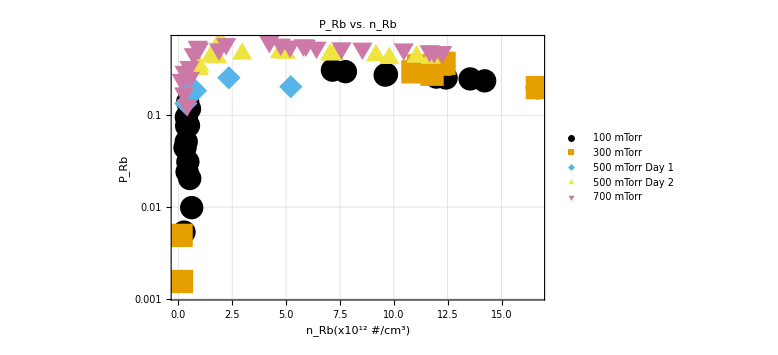

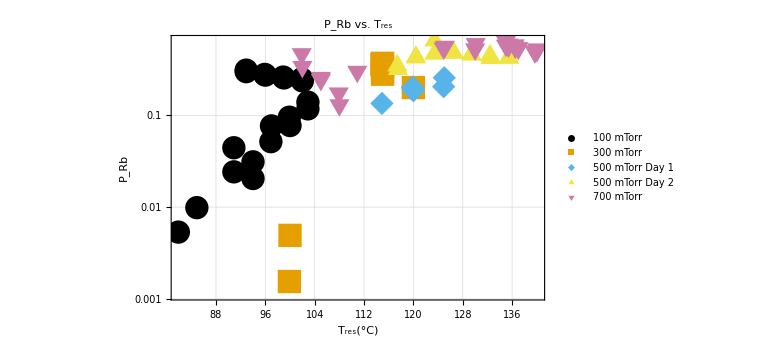

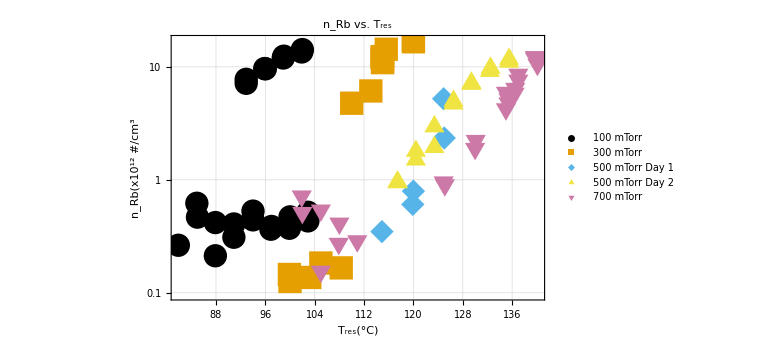

```mathematica
nVsTplotLabels={PlotLabel->"n_Rb vs. T_res",FrameLabel->{"T_res(°C)","n_Rb(x10^12 #/cm^3"}};
nVsBGPplotLabels={PlotLabel->"n_Rb vs. P_N_2",FrameLabel->{"P_N_2(torr)","n_Rb(x10^12 #/cm^3"}};
pVsTplotLabels={PlotLabel->"P_Rb vs. T_res",FrameLabel->{"T_res(°C)","P_Rb"}};
pVsnplotLabels={PlotLabel->"P_Rb vs. n_Rb",FrameLabel->{"n_Rb(x10^12 #/cm^3)","P_Rb"}};
options={GridLines->{Automatic,Automatic},Frame->True,PlotMarkers->{Automatic,24},ImageSize->Large,BaseStyle->{FontSize->24},PlotStyle->colorBlindPallete,PlotRange->{Full,Full}}

var1="n_rb";
var2="p_rb";

ListLogPlot[{Legended[BGP100mTorr[All,{var1,var2}],"100 mTorr"],Legended[BGP300mTorr[All,{var1,var2}],"300 mTorr"],Legended[BGP500mTorrOld[All,{var1,var2},Abs],"500 mTorr Day 1"],Legended[BGP500mTorrNew[All,{var1,var2}],"500 mTorr Day 2"],Legended[BGP700mTorr[All,{var1,var2}],"700 mTorr"]},pVsnplotLabels,options]
var1="CurrTemp(Res)";
var2="p_rb";
ListLogPlot[{Legended[BGP100mTorr[All,{var1,var2}],"100 mTorr"],Legended[BGP300mTorr[All,{var1,var2}],"300 mTorr"],Legended[BGP500mTorrOld[All,{var1,var2},Abs],"500 mTorr Day 1"],Legended[BGP500mTorrNew[All,{var1,var2}],"500 mTorr Day 2"],Legended[BGP700mTorr[All,{var1,var2}],"700 mTorr"]},pVsTplotLabels,options]
var1="CurrTemp(Res)";
var2="n_rb";
ListLogPlot[{Legended[BGP100mTorr[All,{var1,var2}],"100 mTorr"],Legended[BGP300mTorr[All,{var1,var2}],"300 mTorr"],Legended[BGP500mTorrOld[All,{var1,var2},Abs],"500 mTorr Day 1"],Legended[BGP500mTorrNew[All,{var1,var2}],"500 mTorr Day 2"],Legended[BGP700mTorr[All,{var1,var2}],"700 mTorr"]},nVsTplotLabels,options]
```